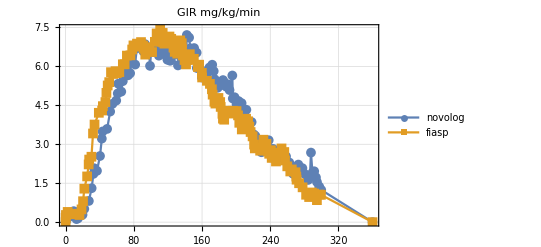

```mathematica
(*   
 IOB Curve Analysis for FIASP and Novolog
Ken Stack, Perceptus.org
Copyright (c) 2017 Perceptus.org

SEE MIT LICENSE TERMS BELOW
*)

(*raw data for both novolog and fiasp are from https://www.ncbi.nlm.nih.gov/pmc/articles/PMC5299522 
this study used an actual insulin pump to deliver basal and bolus for a clamp study, which is the most appropriate for us to use versus studies that mix shots with longer acting insulin *)
(*I used software called PlotDigitizer to pick off about 125 points on each GIR curve to then create IOB and dIOB/dt curves *)
(*glucose clamp data - GIR vs. time for a 0.15 U/kg was actually a reasonable dose to use versus some studies that used 2x more insulin for their bolus dose *)
(*data only goes to 300 minutes but I fit curves until 360 min since GIR wasnt back to basal at that point *)


(* read raw data from csv files*)
rawnovolog=Import["/Users/kennethstack/documents/aspartcsii.csv"];
rawfiasp=Import["/Users/kennethstack/documents/fiaspcsii.csv"];

rawfiasp=Append[rawfiasp,{360,0}];
rawnovolog=Append[rawnovolog,{360,0}];

(*remove any potetnial duplicate points by averaging the different GIR data at the same time.  This only occurs for maybe 1-2 points in the whole set could have probably just eliminated one of them *)

sorted=SortBy[rawfiasp,#[[1]]&];
grouped=GroupBy[sorted,#[[1]]&];
count=1;
fiasp=Range[Length[grouped]];
av=0;
j=0;
(*for duplicated time values replace with a single averaged value for GIR*)
i=1;
While[i<=Length[grouped],
av=0;
For[j=1,j≤Length[grouped[[i]]],j++,av=av+grouped[[i]][[j]][[2]]];
av=av/Length[grouped[[i]]];
fiasp[[count]]={grouped[[i]][[1]][[1]],av};
count++;
i++
]

sorted=SortBy[rawnovolog,#[[1]]&];
grouped=GroupBy[sorted,#[[1]]&];
count=1;
novolog=Range[Length[grouped]];
av=0;
j=0;
(*for duplicated time values replace with a single averaged value for GIR*)
i=1;
While[i<=Length[grouped],
av=0;
For[j=1,j≤Length[grouped[[i]]],j++,av=av+grouped[[i]][[j]][[2]]];
av=av/Length[grouped[[i]]];
novolog[[count]]={grouped[[i]][[1]][[1]],av};
count++;
i++
]
(****Raw GIR Data ****)

ListLinePlot[{novolog,fiasp},PlotTheme->"Detailed",PlotLabel->"GIR mg/kg/min",PlotMarkers->{Automatic, 10},PlotLegends->{"novolog","fiasp"}]
```

```mathematica
(* interpolate for easier manipulation with Order 1 - straight lines between points *)
novosmooth=Interpolation[novolog,InterpolationOrder->1];
fiaspsmooth=Interpolation[fiasp,InterpolationOrder->1];
maxt=novolog[[Length[novolog]]][[1]];
```

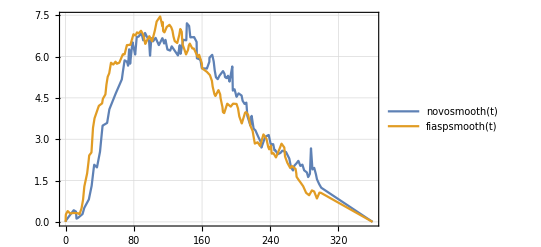

```mathematica
Plot[{novosmooth[t],fiaspsmooth[t]},{t,0,maxt},PlotTheme->"Detailed"]
```

```mathematica
(*calculate total areas under each GIR curve
note they are virtually the same - this means that a unit of fiasp and a unit of novolog will drop bg the same amount - same effect just fiasp is faster *)
aucn=NIntegrate[novosmooth[t],{t,0,novolog[[Length[novolog]]][[1]]}]
aucf=NIntegrate[fiaspsmooth[t],{t,0,fiasp[[Length[fiasp]]][[1]]}]
```

1269.41

1281.96

```mathematica
(*calculate iob curves - Method from Glucose clamp algorithms and insulin time-action profiles - Bequette 
https://www.ncbi.nlm.nih.gov/pubmed/20144413 *)

(* iob (t) = 1- (integral of GIR from 0 to t) / (total GIR AUC)*)
```

```mathematica
novoiob=Interpolation[Table[{t,(1-NIntegrate[novosmooth[s]/aucn,{s,0,t}])*100},{t,0,novolog[[Length[novolog]]][[1]],2}],InterpolationOrder->1];

fiaspiob=Interpolation[Table[{t,(1-NIntegrate[fiaspsmooth[s]/aucf,{s,0,t}])*100},{t,0,fiasp[[Length[fiasp]]][[1]],2}],InterpolationOrder->1];
```

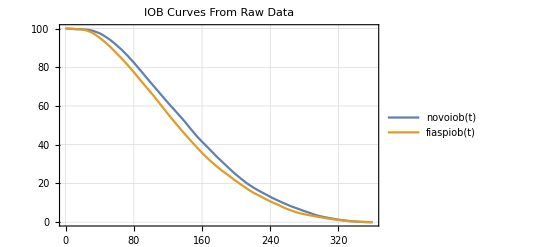

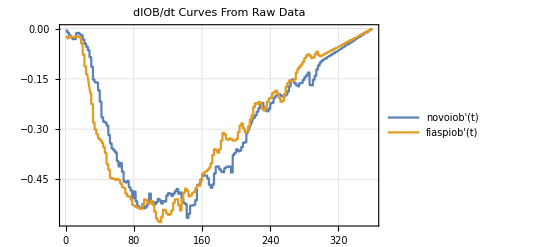

```mathematica
(* plot iob curves and more importantly derivatives *)
Plot[{novoiob[t],fiaspiob[t]},{t,0,maxt},PlotTheme->"Detailed",PlotLabel->"IOB Curves From Raw Data"]
Plot[{novoiob'[t],fiaspiob'[t]},{t,0,maxt},PlotTheme->"Detailed",PlotLabel->"dIOB/dt Curves From Raw Data"]
```

```mathematica
(*IOB Curves*)
(*also calculated the close form derivative this is important for all loop programs *)

(*NOTE Mathematica uses E^(a) - this is the exponential constant e(base of natural logarithms),with numerical value 2.71.... .*)


(**** Define IOB Curves ****)

loopiob[peakActivityTime_,actionDuration_,t_]:=(tau=peakActivityTime*(1-peakActivityTime/actionDuration)/(1-2*peakActivityTime/actionDuration);a=2*tau/actionDuration;S=1/(1-a+(1+a)*Exp[-actionDuration/tau]);
1-S*(1-a)*((t*t/(tau*actionDuration*(1-a))-t/tau-1)*Exp[-t/tau]+1))

dloopiobdt[peakActivityTime_,actionDuration_,t_]:=(tau=peakActivityTime*(1-peakActivityTime/actionDuration)/(1-2*peakActivityTime/actionDuration);a=2*tau/actionDuration;S=1/(1-a+(1+a)*Exp[-actionDuration/tau]);
(-(1 - a))*S*((-(1/tau) + (2*t)/((1 - a)*actionDuration*tau))/E^(t/tau) - 
   (-1 - t/tau + t^2/((1 - a)*actionDuration*tau))/(E^(t/tau)*tau)))

(*define the default curves in Loop (maybe OPENAPS too?) as I understand *)
loopiobfiasp[t_]:=loopiob[55,6*60,t]
loopiobnovo[t_]:=loopiob[75,6*60,t]

(*MDT curves from old days*)
mdtiob4hr[g_,gs_]:=Piecewise[{{0,g-gs≤0},{-3.31*^-8*(g-gs)^4+2.53*^-5*(g-gs)^3-5.51*^-3*(g-gs)^2-9.086*^-2*(g-gs)+99.95, (g-gs) > 0 && (g -gs)<= 240},{0,(g-gs)>240}}];
mdtiob5hr[g_,gs_]:=Piecewise[{{0,g-gs≤0},{-2.95*^-8*(g-gs)^4+2.32*^-5*(g-gs)^3-5.55*^-3*(g-gs)^2+4.49*^-2*(g-gs)+99.3, (g-gs) > 0 && (g -gs)<= 300},{0,(g-gs)>300}}];
```

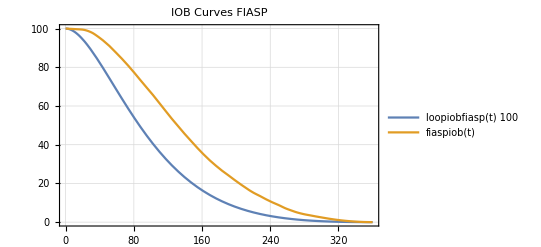

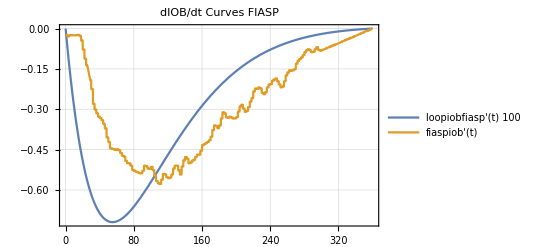

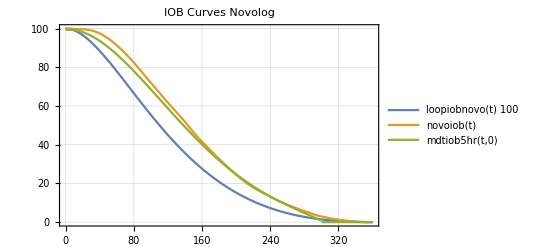

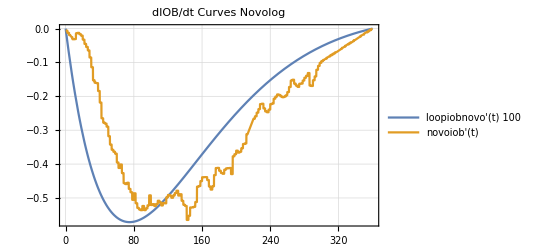

```mathematica
(**********Compare Loop Default Expontential Model to GIR Data***********)
(*Plot IOB curves and Their Derivatives vs. Time *)
Plot[{loopiobfiasp[t]*100,fiaspiob[t]},{t,0,maxt},PlotTheme->"Detailed",PlotLabel->"IOB Curves FIASP"]

Plot[{loopiobfiasp'[t]*100,fiaspiob'[t]},{t,0,maxt},PlotTheme->"Detailed",PlotLabel->"dIOB/dt Curves FIASP"]

Plot[{loopiobnovo[t]*100,novoiob[t],mdtiob5hr[t,0]},{t,0,maxt},PlotTheme->"Detailed",PlotLabel->"IOB Curves Novolog"]

Plot[{loopiobnovo'[t]*100,novoiob'[t]},{t,0,maxt},PlotTheme->"Detailed",PlotLabel->"dIOB/dt Curves Novolog"]
```

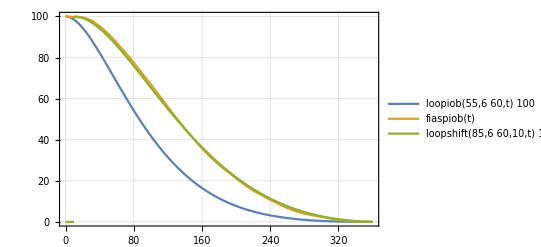

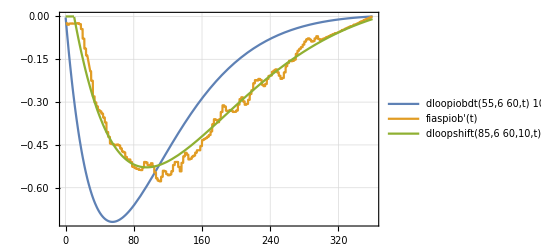

```mathematica
(*couple of comments
- the exponential curve is quite nice but it missed the initial delay - you get a strong negative bg velocity from minute zero, which I dont think is physical.
- it seems agressive that the peak would be at 55 min -  an IOB curve is usually calculated from Pharmacodynamics (BG changes due to insulin) not PharmacoKinetics (insulin concentration)
- From Novo Nordisks FIASP data the peak time for GIR was 124 min, and the peak time for concentration was 63 min.  In Heise et all with a pump peak time was 114 min for GIR and 55 min for concentration.   so this curve from Loop with a peak of 55 min - if Im understanding it right - has a time of action that is equal to concentration, and less then half the GIR peak time from the literature.  This seems REALLY fast  -at best it should be between.  It is faster then Afreeza, which we know is much faster then FIASP. 
- I think as I said above its really key to compare the derivative curves for speed as this is what drives the change in BG minute to minute ie BG velocity is proportional to diob/dt in all of our simple models 
- the Loop novolog curve looks even more extreme on a relative basis with a peak of 75 min - are people seeing such fast novolog action ? What changed from the old Walsh Curves ?  They result in almost completely different behavior.  The new exponrtential curves are incredibly fast on a relative scale.  This would say that the bolus wizard curves in most pumps including MDT are wrong.
- on thing to note - the function form that has been chosen here gives an "instant" BG veloctiy (negative of course) the moment you take insulin.  There is no delay - if you look at both the GIR and even the concentration data there is a delay - that should be added at some point - PARTICULARLY for novolog 
- I realize that some people may feel strongly that the IOB effect should be proportional to concentration (PK) rather then glood glucose action (PD) - we can see from the GIR data it is not.  While there is confusion out there the definition of IOB really is PD, not PK.   Its really a question of how you want to use IOB.  Glucodyn and Bolus Wizard math in general assumes IOB is action on BG.  
- I think one big learning from the last few years is that simply fitting the IOB % is not enough - one MUST make sure the derivative is smooth and reasonable.  
- The "fixing" of the action curve as we are doing is something I think that needs to go away longer term.  now that we have CGM data and lots of it, we should be creating individual curves for people based on real insulin action - yes the models get slightly more complicated but there is no way 2 people have the exact same action curves - IMHO  - but thats for ongoing research
*)

(******Add a Shift to Exponential Model and Fit Parameters *******)

(* Fit was dont by eye - can do it via optimization but I doubt it matters *)
(* used an initial delay parameter based on discussions between K. DiSimonie and B. Buckingham of Stanford - 10 min for Fiasp, 20 min for Novolog *)

(*for Fiasp, decent fit with peak of 85 min, delay of 10 min *)
(* for novolog, delay of 20 min, peak of 92 min *)
(* again, room here for optimization *)



loopshift[peakActivityTime_,actionDuration_,initialDelay_,t_]:=If[t<initialDelay,0,loopiob[peakActivityTime,actionDuration,t-initialDelay]]
dloopshift[peakActivityTime_,actionDuration_,initialDelay_,t_]:=If[t<initialDelay,0,dloopiobdt[peakActivityTime,actionDuration,t-initialDelay]]

Plot[{loopiob[55,6*60,t]*100,fiaspiob[t],loopshift[85,6*60,10,t]*100},{t,0.1,maxt},PlotTheme->"Detailed",PlotRange->Full]
Plot[{dloopiobdt[55,6*60,t]*100,fiaspiob'[t],dloopshift[85,6*60,10,t]*100},{t,0.1,maxt},PlotTheme->"Detailed"]

(*blue curves are the original loop parameters *)

(* FIASP Fit *)
```

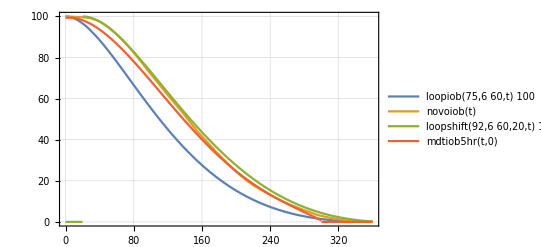

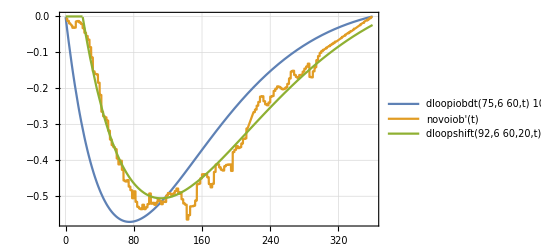

```mathematica
Plot[{loopiob[75,6*60,t]*100,novoiob[t],loopshift[92,6*60,20,t]*100,mdtiob5hr[t,0]},{t,0.1,maxt},PlotTheme->"Detailed",PlotRange->Full]
Plot[{dloopiobdt[75,6*60,t]*100,novoiob'[t],dloopshift[92,6*60,20,t]*100},{t,0.1,maxt},PlotTheme->"Detailed"]


(*Novolog Fit *)
```

```mathematica
(*matching the IOB curve is one thing - matching the derivative of the iob curve I think is even more important - thats what gives us our local BG velocity PLEASE REMEMBER all of this is a massive approximation and physiologically not quite right as it ignores all sorts of things like liver, renal, counter regulatory and the body's constant changes even in insulin absorbtion etc *)
```

```mathematica
(*The MIT License (MIT)

Copyright (c) 2017 Perceptus.org

Permission is hereby granted,free of charge,to any person obtaining a copy
of this software and associated documentation files (the "Software"),to deal
in the Software without restriction,including without limitation the rights
to use,copy,modify,merge,publish,distribute,sublicense,and/or sell
copies of the Software,and to permit persons to whom the Software is
furnished to do so,subject to the following conditions:The above copyright notice and this permission notice shall be included in all
copies or substantial portions of the Software.

THE SOFTWARE IS PROVIDED "AS IS",WITHOUT WARRANTY OF ANY KIND,EXPRESS OR
IMPLIED,INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY,FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT.IN NO EVENT SHALL THE
AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM,DAMAGES OR OTHER
LIABILITY,WHETHER IN AN ACTION OF CONTRACT,TORT OR OTHERWISE,ARISING FROM,OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE
SOFTWARE.*)
```